### Mass Matrix - 1 Flavour Scenario for (Generalized) Clockwork

```mathematica
K = 19;qt=0;a=1;q=-2.50;
(* qt is q^∼ (Majorana mass term), K is the number of sites and a is mass term (m) and q is Dirac mass term in cw fermions. *)
```

```mathematica
cw= Table[0,{x,2K+1},{y,2K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
i=1;While[i<2K+2,{cw[[i,i]] = qt };i++]
i=1;While[i<K+1,{cw[[i,K+i]] = a-0*i*0.05};i++]
i=1;While[i<K+1,{cw[[K+i,i]] = a -0*i*0.05};i++]
i=1;While[i<K+1,{cw[[i,K+1+i]] = q-i*0.1};i++]
i=1;While[i<K+1,{cw[[K+1+i,i]] = q-i*0.1};i++]

(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
cw;
```

```mathematica
ev = Eigenvalues[cw];
```

```mathematica
Kcw = cw[[1;;K,K+1;;2K+1]]
```

(1. | -2.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | -2.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | -2.8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | -2.9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | -3.1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.7 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -3.9 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -4. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -4.1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -4.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -4.3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | -4.4)

```mathematica
NullSpace[Kcw]
```

(0.924044 | 0.355402 | 0.13163 | 0.0470108 | 0.0162106 | 0.00540354 | 0.00174308 | 0.000544712 | 0.000165064 | 0.0000485483 | 0.0000138709 | 3.85304×10^-6 | 1.04136×10^-6 | 2.74043×10^-7 | 7.02673×10^-8 | 1.75668×10^-8 | 4.28459×10^-9 | 1.02014×10^-9 | 2.37242×10^-10 | 5.39186×10^-11)

```mathematica
%[[-1]][[-1]]
```

5.39186×10^-11

```mathematica
ev1 = -Sort[ev];
```

```mathematica
Y1 = Eigenvectors[cw];
```

```mathematica
H1= Inverse[Y1];
```

```mathematica
Ev1 = Sort[Abs[ ev1]];
```

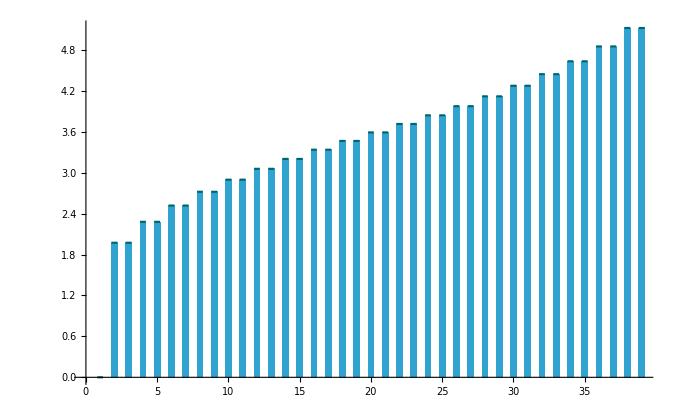

```mathematica
DiscretePlot[Ev1⟦i⟧,{i,1,2 K+1},PlotStyle->Directive[RGBColor[0.,0.4,0.42],Opacity[1.],AbsoluteThickness[1.545]],ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,0.6,0.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"n","M(TeV)"},LabelStyle->Directive[Bold,Medium],PlotRange->{0,All}, Epilog->{Text[ "",Scaled[{0.8,0.95}]],Text["",Scaled[{0.8,0.9}]]},FrameTicks->{Automatic,Automatic}]
```

```mathematica
Rn1 = H1[[2K+1,All]];
(* Change of basis from Subscript[ψ^c, R,r]  to eigenvector of cw2 in interaction term. *)
```

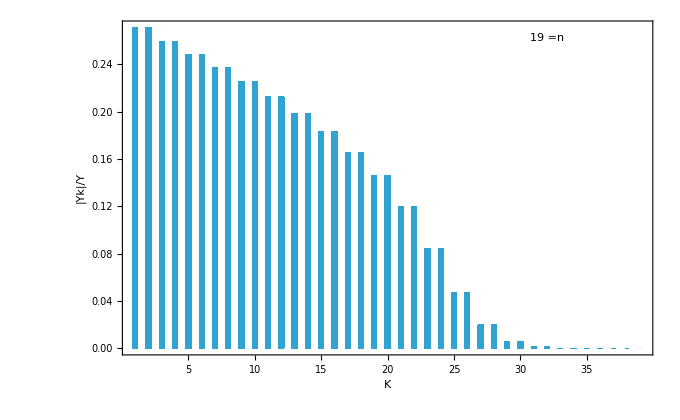

```mathematica
DiscretePlot[Abs[Rn1[[i]]],{i,1,2*K+1},ExtentSize->0.4,ImageSize->680,BaseStyle->{FontFamily->"LM Roman 10",FontSize->10},Frame->True,PlotStyle-> {Opacity[0.9,RGBColor[0.1,.6,.8]],Directive[AbsoluteThickness[0]]},
Filling->Axis,FillingStyle->Opacity[0.9,RGBColor[0.1,.6,.8]],FrameTicks->{Automatic,Automatic},FrameLabel->{"K","|Yk|/Y"},LabelStyle->Directive[Bold, Medium],PlotRange->All,Epilog->{Text["",Scaled[{0.8,0.90}]],Text["",Scaled[{0.8,0.95}]],{Text[K"=n",Scaled[{.8,.95}]]}}]
```

### 3 Flavour Scenario

```mathematica
q=4;K=15;v=0.173;p=0.1*v;
 (*K is the number of sites parameter, p is the coupling strength between SM neutrino and Subscript[R, n], and q is neighbouring coupling strength.*)
```

```mathematica
cw= Table[0,{x,K+1},{y,K+1}];
(* Dummy matrix to form clockwork mass matrix *)
```

```mathematica
i=2;While[i<K+2,{cw[[i,i]] = 1 };i++]
i=1;While[i<K+1,{cw[[1+i,i]] = -q-(K+1-i)*0.0};i++]
cw2=cw;cw3=cw;
(* Clockwork mass matrix in Ψ basis, where Ψ = ( Subscript[ψ, L,0],Subscript[ψ, L,1],Subscript[ψ, L,2], ..... Subscript[ψ, L,K-1],Subscript[ψ^c, R,0],Subscript[ψ^c, R,1], .... Subscript[ψ^c, R,K] *)
```

```mathematica
cw[[1,1]]=p;cw2[[1,1]]=1.01p;cw3[[1,1]]=0.63p; (*3 CW chains for 3 masses.*)
```

```mathematica
cw3;
```

```mathematica
{u1,m1,v1}=SingularValueDecomposition[SetPrecision[cw,20]];{u2,m2,v2}=SingularValueDecomposition[SetPrecision[cw2,20]];{u3,m3,v3}=SingularValueDecomposition[SetPrecision[cw3,20]];
```

```mathematica
a1=m1[[-1,-1]]
a2=m2[[-1,-1]]
a3=m3[[-1,-1]] (*Three Masses produced*)
```

1.5600105621619291422×10^-11

1.5756103518417210761×10^-11

9.8281256737636976397×10^-12

```mathematica
(a2^2-a1^2)*Power[10,24](*Mass squared differences Subscript[Δm^2, 21].*)
(a3^2-a2^2)*Power[10,24] (*Mass squared differences Subscript[Δm^2, 32].*)
```

4.8915026774013894

-151.6627438237860725